```mathematica
(*Parameters*)
qcircle1=Graphics[Circle[{0,5*√2},10,{-Pi/4,-3*Pi/4}]];
qcircle2=Graphics[{Red,Circle[{0,-5*√2},10,{Pi/4,3*Pi/4}]}];
circle = ContourPlot[(x^2+(y)^2)==25,{x,-20,20},{y,-20,20},Axes->False];
square=ParametricPlot[{5*{-1/(√2)+t/(√2),-1/(√2)-t/(√2)},5*{1/(√2)+t/(√2),-1/(√2)+t/(√2)},5*{1/(√2)+t/(√2),1/(√2)-t/(√2)},5*{-1/(√2)+t/(√2),1/(√2)+t/(√2)}},{t,-1,1},PlotStyle->{Blue,Blue,Blue,Blue}];

textA=Graphics[Text[Style["A",20],{-(5 √(7/2))/2,5/(2 √2)},{0.5,-0.5}]];
textB=Graphics[Text[Style["B",20],{(5 √(7/2))/2,5/(2 √2)},{-0.5,-0.5}]];
textC=Graphics[Text[Style["C",20],{0,-5*√2},{0,1}]];
textD=Graphics[Text[Style["D",20],{0,0},{1,1}]];
textE=Graphics[Text[Style["E",20],{0,5},{1,1}]];
textF=Graphics[Text[Style["F",20],{0,3},{1,1}]];
Line1=Plot[{y=5/(2 √2)},{x,-(5 √(7/2))/2,(5 √(7/2))/2}];
Line2=Plot[y=(5 √7)/7 x-5 √2,{x,0,(5 √(7/2))/2}];
Line3=Plot[y=-(5 √7)/7 x-5 √2,{x,-(5 √(7/2))/2,0}];
Line4=Plot[y=-(√7)/7 x,{x,-(5 √(7/2))/2,0}];
Line5=Plot[y=(√7)/7 x,{x,0,(5 √(7/2))/2}];
```

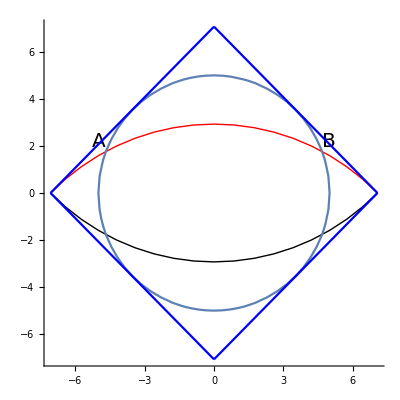

```mathematica
(*Solve using integration*)
(* Rotate axis so that the intergration would be more direct*)
Show[qcircle1,qcircle2,circle,textA,textB,square,Axes->True]
```

```mathematica
(*Calculate crossing point for two circle 
 First Circle: (x^2+(y+5*√2)^2)==100;    Seconde Circle: (x)^2+(y)^2==25*) 
Solve[(x^2+(y+5*√2)^2)==100 && (x)^2+(y)^2==25, {x,y}]
```

{{x→-(5 √(7/2))/2,y→5/(2 √2)},{x→(5 √(7/2))/2,y→5/(2 √2)}}

```mathematica
(*Now, we have the upper limit and lower limit, do intergration to find half of the area we seek*)
N[Integrate[√(25-(x)^2)-(√(100-x^2)-5*√2),{x,-(5 √(7/2))/2,(5 √(7/2))/2}]];
```

```mathematica
(*Total area*)
2*%
```

29.2763

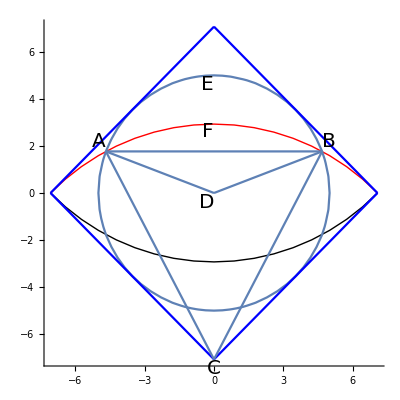

```mathematica
(*Solve using trigonometry*)
Show[qcircle1,qcircle2,circle,square,textA,textB,textC,textD,textE,textF,Line1,Line2,Line3,Line4,Line5,Axes->True]
```

```mathematica
(*What we know*)
(*length of AC, AD, DC*)
(*Area_AFBEA=Area_ABEA-Area_ABFA*)
(*Area_ABEA=Area_ADBEA-Area_ABDA*)
(*Area_ABFA=Area_ACBFA-Area_ACBA*)
AC=10;
AD=5;
DC=5 √2;
(*Now, lets get to work*)
(*Area_ABFA*)
∠ACD=ArcCos[(AC^2+DC^2-AD^2)/(2*AC*DC)];
ACBFA=(2*N[∠ACD])/(2π)*π*10^2;
ACBA=N[1/2*AC*AC*Sin[2*∠ACD]];
ABFA=ACBFA-ACBA;
(*Area_ABEA*)
∠ADC=ArcCos[(AD^2+DC^2-AC^2)/(2*AD*DC)];
∠ADB=2*(π-∠ADC);
ADBEA=(∠ADB)/(2*π)*π*5^2;
ADBA=1/2*AD^2*Sin[∠ADB];
ABEA=N[ADBEA-ADBA];
(*Area_AFBEA*)
AFBEA=(ABEA-ABFA);
(*Total_area*)
2*%
```

29.2763